# Catalan Numbers

Peter Cullen Burbery

I analyze several applications of Catalan numbers.

## Catalan Sequences

Find the 20th totally balanced binary sequence with five 1’s:

```mathematica
CatalanUnrank[5,20]
```

{0,0,1,0,1,0,1,1,0,1}

Find the number of totally balanced binary sequences with five 1's:

```mathematica
CatalanNumber[5]
```

42

Show the totally balanced binary sequences with five 1’s:

```mathematica
CatalanUnrank[5,#]&/@Range[0,CatalanNumber[5]-1]
```

{{0,0,0,0,0,1,1,1,1,1},{0,0,0,0,1,0,1,1,1,1},{0,0,0,0,1,1,0,1,1,1},{0,0,0,0,1,1,1,0,1,1},{0,0,0,0,1,1,1,1,0,1},{0,0,0,1,0,0,1,1,1,1},{0,0,0,1,0,1,0,1,1,1},{0,0,0,1,0,1,1,0,1,1},{0,0,0,1,0,1,1,1,0,1},{0,0,0,1,1,0,0,1,1,1},{0,0,0,1,1,0,1,0,1,1},{0,0,0,1,1,0,1,1,0,1},{0,0,0,1,1,1,0,0,1,1},{0,0,0,1,1,1,0,1,0,1},{0,0,1,0,0,0,1,1,1,1},{0,0,1,0,0,1,0,1,1,1},{0,0,1,0,0,1,1,0,1,1},{0,0,1,0,0,1,1,1,0,1},{0,0,1,0,1,0,0,1,1,1},{0,0,1,0,1,0,1,0,1,1},{0,0,1,0,1,0,1,1,0,1},{0,0,1,0,1,1,0,0,1,1},{0,0,1,0,1,1,0,1,0,1},{0,0,1,1,0,0,0,1,1,1},{0,0,1,1,0,0,1,0,1,1},{0,0,1,1,0,0,1,1,0,1},{0,0,1,1,0,1,0,0,1,1},{0,0,1,1,0,1,0,1,0,1},{0,1,0,0,0,0,1,1,1,1},{0,1,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,1,0,1,1},{0,1,0,0,0,1,1,1,0,1},{0,1,0,0,1,0,0,1,1,1},{0,1,0,0,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,1,0,0,1,1},{0,1,0,0,1,1,0,1,0,1},{0,1,0,1,0,0,0,1,1,1},{0,1,0,1,0,0,1,0,1,1},{0,1,0,1,0,0,1,1,0,1},{0,1,0,1,0,1,0,0,1,1},{0,1,0,1,0,1,0,1,0,1}}

## Grouping Symbols

Find all sets of 3 parentheses that are balanced:

```mathematica
AllBalancedGroupingSymbols[{"(",")"},3]
```

{((())),(()()),(())(),()(()),()()()}

### Parentheses ()

```mathematica
AllBalancedGroupingSymbols[{"(",")"},4]
```

{(((()))),((()())),((())()),((()))(),(()(())),(()()()),(()())(),(())(()),(())()(),()((())),()(()()),()(())(),()()(()),()()()()}

### Angle Brackets ⟨⟩

```mathematica
AllBalancedGroupingSymbols[{"⟨","⟩"},4]
```

{⟨⟨⟨⟨⟩⟩⟩⟩,⟨⟨⟨⟩⟨⟩⟩⟩,⟨⟨⟨⟩⟩⟨⟩⟩,⟨⟨⟨⟩⟩⟩⟨⟩,⟨⟨⟩⟨⟨⟩⟩⟩,⟨⟨⟩⟨⟩⟨⟩⟩,⟨⟨⟩⟨⟩⟩⟨⟩,⟨⟨⟩⟩⟨⟨⟩⟩,⟨⟨⟩⟩⟨⟩⟨⟩,⟨⟩⟨⟨⟨⟩⟩⟩,⟨⟩⟨⟨⟩⟨⟩⟩,⟨⟩⟨⟨⟩⟩⟨⟩,⟨⟩⟨⟩⟨⟨⟩⟩,⟨⟩⟨⟩⟨⟩⟨⟩}

### Square Brackets []

```mathematica
AllBalancedGroupingSymbols[{"[","]"},4]
```

{[[[[]]]],[[[][]]],[[[]][]],[[[]]][],[[][[]]],[[][][]],[[][]][],[[]][[]],[[]][][],[][[[]]],[][[][]],[][[]][],[][][[]],[][][][]}

### Curly Brackets {}

```mathematica
AllBalancedGroupingSymbols[{"{","}"},4]
```

{{{{{}}}},{{{}{}}},{{{}}{}},{{{}}}{},{{}{{}}},{{}{}{}},{{}{}}{},{{}}{{}},{{}}{}{},{}{{{}}},{}{{}{}},{}{{}}{},{}{}{{}},{}{}{}{}}

### Floor Brackets ⌊⌋

```mathematica
AllBalancedGroupingSymbols[{"⌊","⌋"},4]
```

{⌊⌊⌊⌊⌋⌋⌋⌋,⌊⌊⌊⌋⌊⌋⌋⌋,⌊⌊⌊⌋⌋⌊⌋⌋,⌊⌊⌊⌋⌋⌋⌊⌋,⌊⌊⌋⌊⌊⌋⌋⌋,⌊⌊⌋⌊⌋⌊⌋⌋,⌊⌊⌋⌊⌋⌋⌊⌋,⌊⌊⌋⌋⌊⌊⌋⌋,⌊⌊⌋⌋⌊⌋⌊⌋,⌊⌋⌊⌊⌊⌋⌋⌋,⌊⌋⌊⌊⌋⌊⌋⌋,⌊⌋⌊⌊⌋⌋⌊⌋,⌊⌋⌊⌋⌊⌊⌋⌋,⌊⌋⌊⌋⌊⌋⌊⌋}

### Ceiling Brackets ⌈⌉

```mathematica
AllBalancedGroupingSymbols[{"⌈","⌉"},4]
```

{⌈⌈⌈⌈⌉⌉⌉⌉,⌈⌈⌈⌉⌈⌉⌉⌉,⌈⌈⌈⌉⌉⌈⌉⌉,⌈⌈⌈⌉⌉⌉⌈⌉,⌈⌈⌉⌈⌈⌉⌉⌉,⌈⌈⌉⌈⌉⌈⌉⌉,⌈⌈⌉⌈⌉⌉⌈⌉,⌈⌈⌉⌉⌈⌈⌉⌉,⌈⌈⌉⌉⌈⌉⌈⌉,⌈⌉⌈⌈⌈⌉⌉⌉,⌈⌉⌈⌈⌉⌈⌉⌉,⌈⌉⌈⌈⌉⌉⌈⌉,⌈⌉⌈⌉⌈⌈⌉⌉,⌈⌉⌈⌉⌈⌉⌈⌉}

### Double Square Brackets ⟦⟧]

```mathematica
AllBalancedGroupingSymbols[{"⟦","⟧"},4]
```

{⟦⟦⟦⟦⟧⟧⟧⟧,⟦⟦⟦⟧⟦⟧⟧⟧,⟦⟦⟦⟧⟧⟦⟧⟧,⟦⟦⟦⟧⟧⟧⟦⟧,⟦⟦⟧⟦⟦⟧⟧⟧,⟦⟦⟧⟦⟧⟦⟧⟧,⟦⟦⟧⟦⟧⟧⟦⟧,⟦⟦⟧⟧⟦⟦⟧⟧,⟦⟦⟧⟧⟦⟧⟦⟧,⟦⟧⟦⟦⟦⟧⟧⟧,⟦⟧⟦⟦⟧⟦⟧⟧,⟦⟧⟦⟦⟧⟧⟦⟧,⟦⟧⟦⟧⟦⟦⟧⟧,⟦⟧⟦⟧⟦⟧⟦⟧}

### Bracketing Bars ||

```mathematica
AllBalancedGroupingSymbols[{"|","|"},4]
```

{⌊⌊⌊⌊⌋⌋⌋⌋,⌊⌊⌊⌋⌊⌋⌋⌋,⌊⌊⌊⌋⌋⌊⌋⌋,⌊⌊⌊⌋⌋⌋⌊⌋,⌊⌊⌋⌊⌊⌋⌋⌋,⌊⌊⌋⌊⌋⌊⌋⌋,⌊⌊⌋⌊⌋⌋⌊⌋,⌊⌊⌋⌋⌊⌊⌋⌋,⌊⌊⌋⌋⌊⌋⌊⌋,⌊⌋⌊⌊⌊⌋⌋⌋,⌊⌋⌊⌊⌋⌊⌋⌋,⌊⌋⌊⌊⌋⌋⌊⌋,⌊⌋⌊⌋⌊⌊⌋⌋,⌊⌋⌊⌋⌊⌋⌊⌋}

### Bracketing Bars ‖‖

```mathematica
AllBalancedGroupingSymbols[{"‖","‖"},4]
```

{‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖}

### String Template <*…*> symbols

```mathematica
AllBalancedGroupingSymbols[{"<*","|*>"},4]
```

{<*<*<*<*|*>|*>|*>|*>,<*<*<*|*><*|*>|*>|*>,<*<*<*|*>|*><*|*>|*>,<*<*<*|*>|*>|*><*|*>,<*<*|*><*<*|*>|*>|*>,<*<*|*><*|*><*|*>|*>,<*<*|*><*|*>|*><*|*>,<*<*|*>|*><*<*|*>|*>,<*<*|*>|*><*|*><*|*>,<*|*><*<*<*|*>|*>|*>,<*|*><*<*|*><*|*>|*>,<*|*><*<*|*>|*><*|*>,<*|*><*|*><*<*|*>|*>,<*|*><*|*><*|*><*|*>}

### Association Template <*…*> symbols

```mathematica
AllBalancedGroupingSymbols[{"<|","|>"},4]
```

{<|<|<|<||>|>|>|>,<|<|<||><||>|>|>,<|<|<||>|><||>|>,<|<|<||>|>|><||>,<|<||><|<||>|>|>,<|<||><||><||>|>,<|<||><||>|><||>,<|<||>|><|<||>|>,<|<||>|><||><||>,<||><|<|<||>|>|>,<||><|<||><||>|>,<||><|<||>|><||>,<||><||><|<||>|>,<||><||><||><||>}

## Mountain Range

I made a function that will make all mountain ranges named DyckPaths:

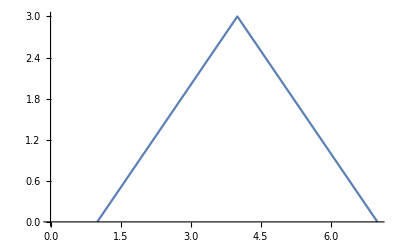
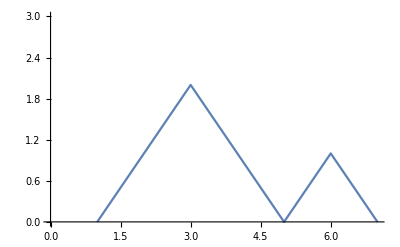
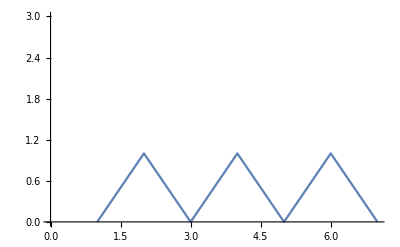
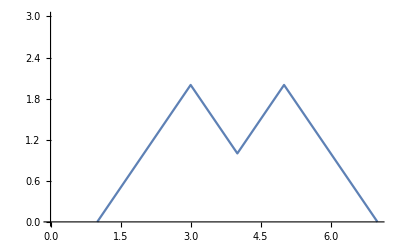
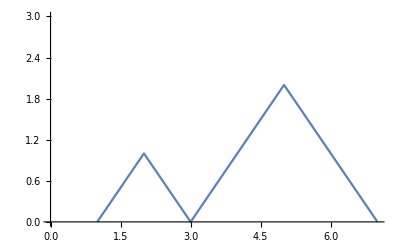
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Multicolumn[DyckPaths[3]]
```

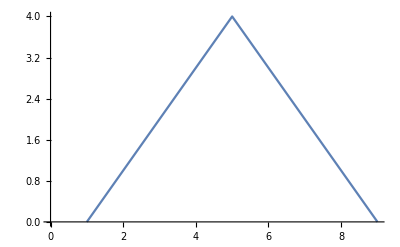
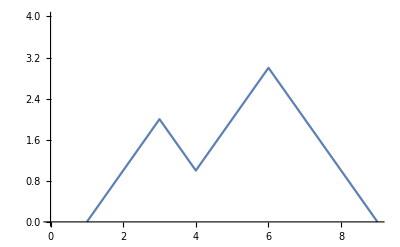
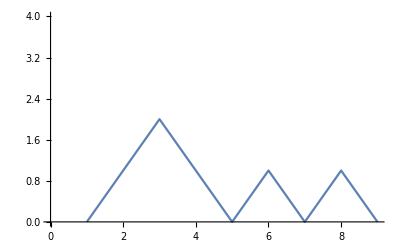
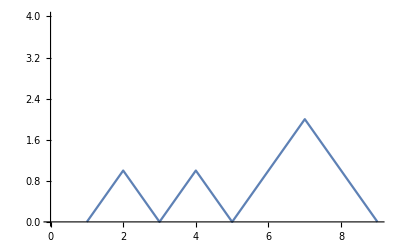
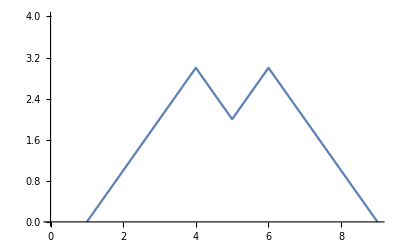
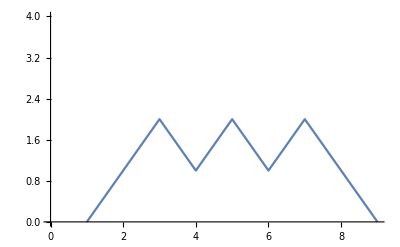
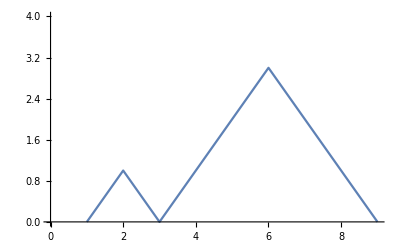
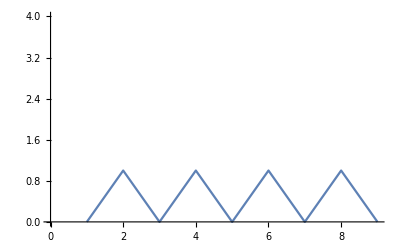
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[DyckPaths[4]]
```

## Walks above or below the diagonal

I made a function that plots all walks above or below the diagonal.

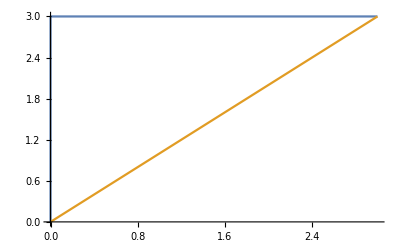
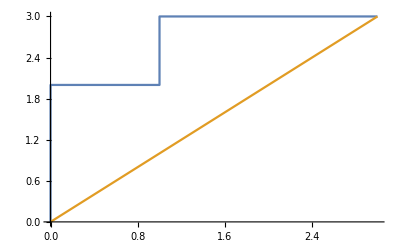
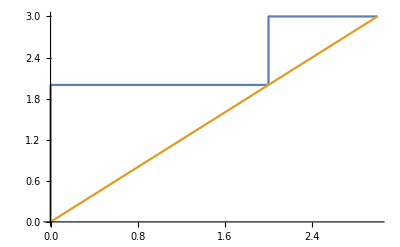
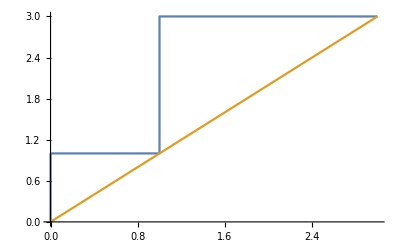
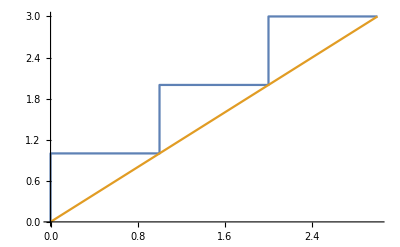
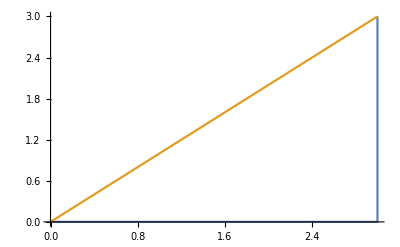
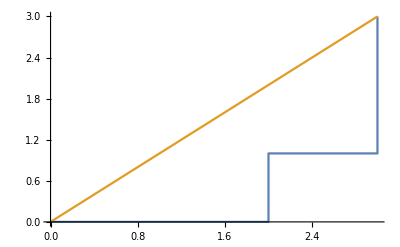
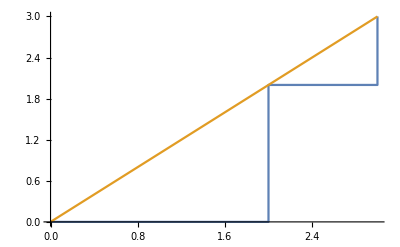

```mathematica
DiagonalWalkPlot[3,{1,1}]
```

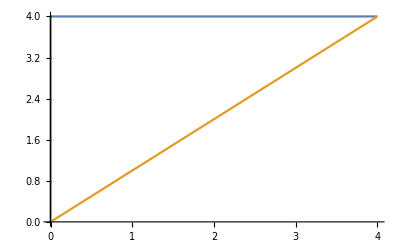
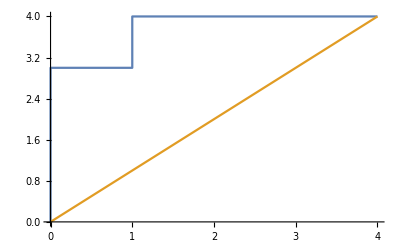
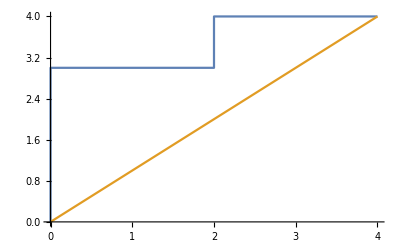
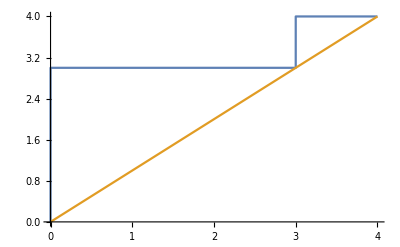
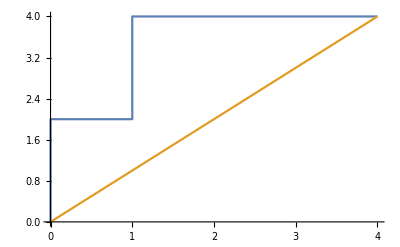
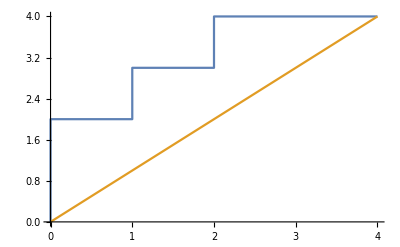
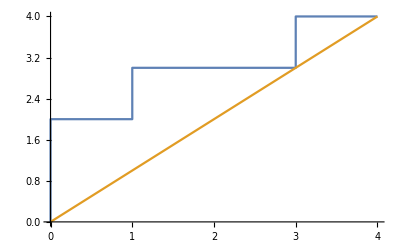
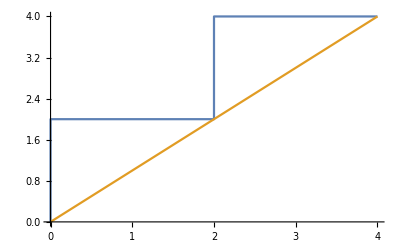

```mathematica
DiagonalWalkPlot[4,{1,1}]
```

## Parenthesized Expressions

I made another function that calculates the parenthesized expressions with a certain number of variables.

```mathematica
ParenthesizedExpressions[4,{b,c,d,f}]
```

{b⊕(c⊕(d⊕f)),b⊕((c⊕d)⊕f),(b⊕c)⊕(d⊕f),(b⊕(c⊕d))⊕f,((b⊕c)⊕d)⊕f}

```mathematica
ParenthesizedExpressions[5,{b,c,d,f,h}]
```

{b⊕(c⊕(d⊕(f⊕h))),b⊕(c⊕((d⊕f)⊕h)),b⊕((c⊕d)⊕(f⊕h)),b⊕((c⊕(d⊕f))⊕h),b⊕(((c⊕d)⊕f)⊕h),(b⊕c)⊕(d⊕(f⊕h)),(b⊕c)⊕((d⊕f)⊕h),(b⊕(c⊕d))⊕(f⊕h),((b⊕c)⊕d)⊕(f⊕h),(b⊕(c⊕(d⊕f)))⊕h,(b⊕((c⊕d)⊕f))⊕h,((b⊕c)⊕(d⊕f))⊕h,((b⊕(c⊕d))⊕f)⊕h,(((b⊕c)⊕d)⊕f)⊕h}

## Full Binary Trees

I made a function to list all full binary trees with n leaves.

```mathematica
FullBinaryTrees[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FullBinaryTrees[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Regular Polygon Triangulations

Catalan numbers are also related to triangulations of regular polygons:

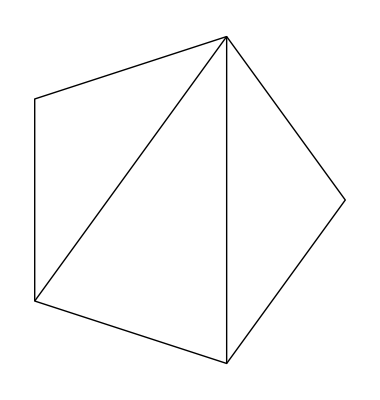
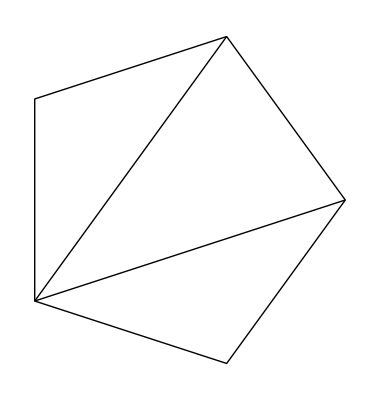
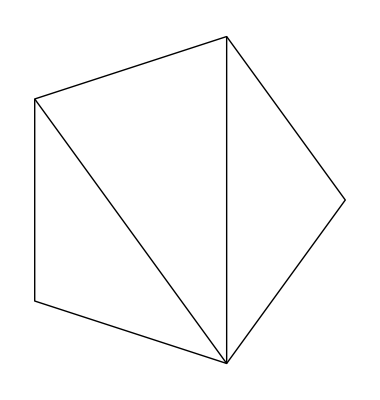
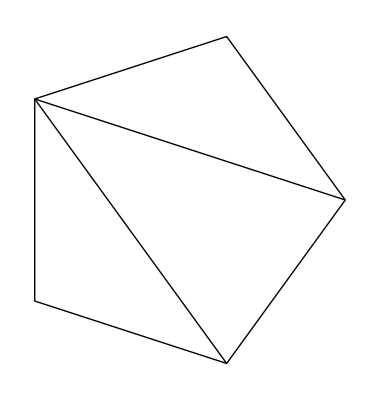
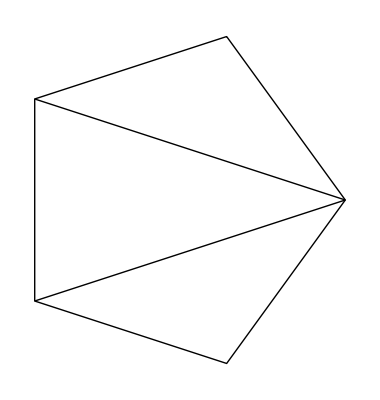

```mathematica
FindRegularPolygonTriangulations[5]
```

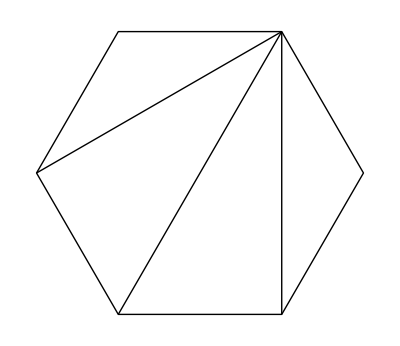
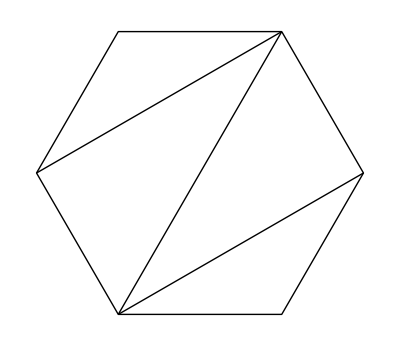
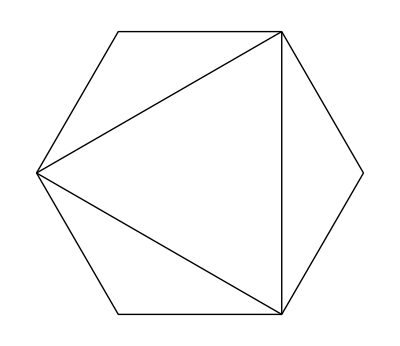
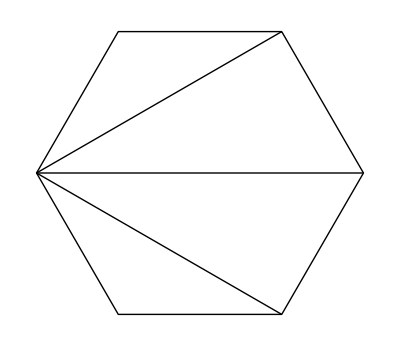
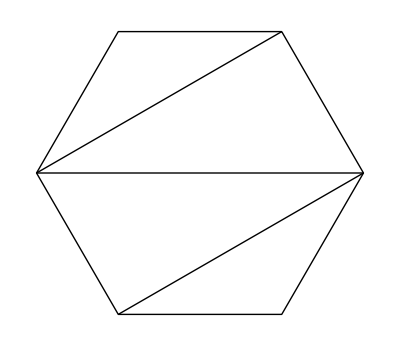
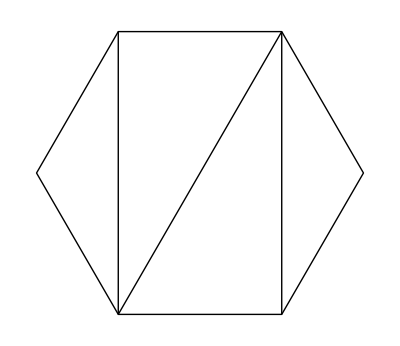
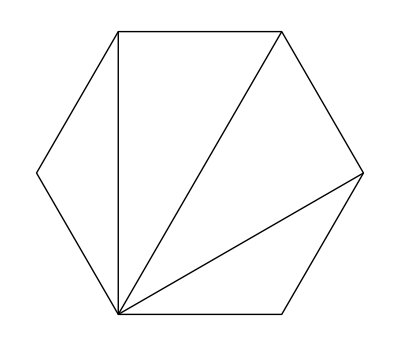
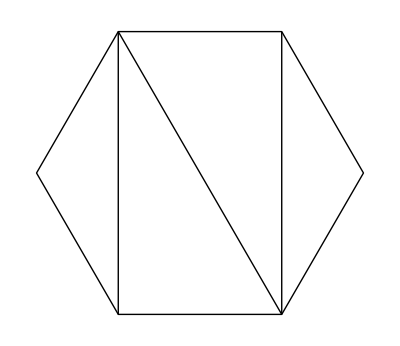

```mathematica
FindRegularPolygonTriangulations[6]
```